```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
SetDirectory[NotebookDirectory[]];
```

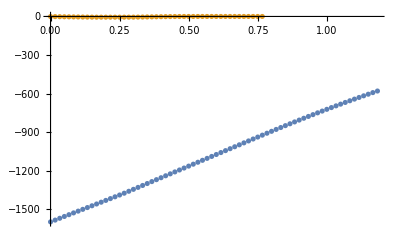

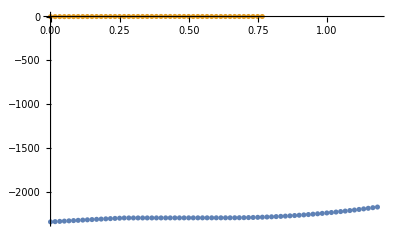

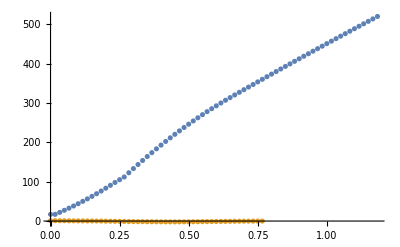

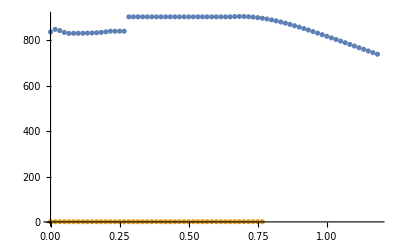

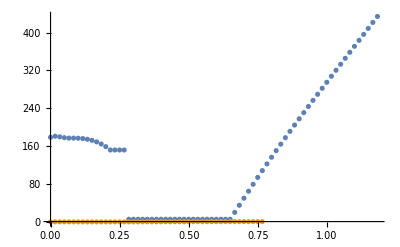

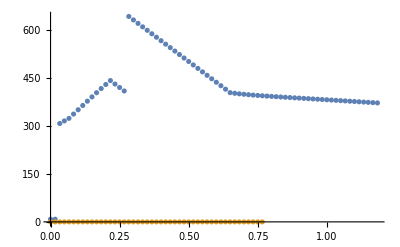

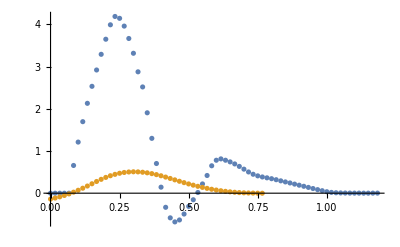

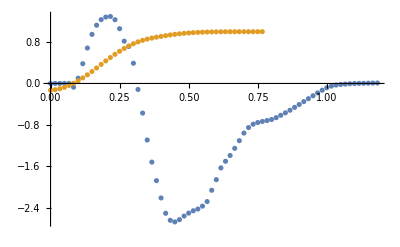

```mathematica
{frame, ball, inputs, car} = #[[1;;-1]]& /@ ImportPhysicsTickJSONEpisode["aerial_turn.json"];
frame = frame-frame[[1]];
t = frame * 1/120.0;
x = #["location"] & /@ car;
v = #["velocity"] & /@ car;
w = #["angular_velocity"] & /@ car;
a = (v[[2;;-1]] - v[[1;;-2]])/(t[[2;;-1]] - t[[1;;-2]]);

data = Import["aerial_turn_simulation.csv"];
data[[All,1]] -= data[[1, 1]];
ListPlot[{
Transpose[{t, x[[All, 1]]}],
data[[All, {1,2}]]
}, PlotRange->All]
ListPlot[{
Transpose[{t, x[[All, 2]]}],
data[[All, {1,3}]]
}, PlotRange->All]
ListPlot[{
Transpose[{t, x[[All, 3]]}],
data[[All, {1,4}]]
}, PlotRange->All]

ListPlot[{
Transpose[{t, v[[All, 1]]}],
data[[All, {1,5}]]
}, PlotRange->All]
ListPlot[{
Transpose[{t, v[[All, 2]]}],
data[[All, {1,6}]]
}, PlotRange->All]
ListPlot[{
Transpose[{t, v[[All, 3]]}],
data[[All, {1,7}]]
}, PlotRange->All]

ListPlot[{
Transpose[{t, w[[All, 1]]}],
data[[All, {1,8}]]
}, PlotRange->All]
ListPlot[{
Transpose[{t, w[[All, 2]]}],
data[[All, {1,9}]]
}, PlotRange->All]
ListPlot[{
Transpose[{t, w[[All, 3]]}],
data[[All, {1,10}]]
}, PlotRange->All]
```